### Load Data

-139.68

0.

-17.6532

-198.915

0.

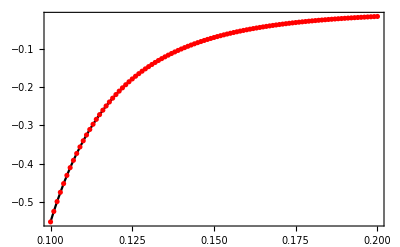

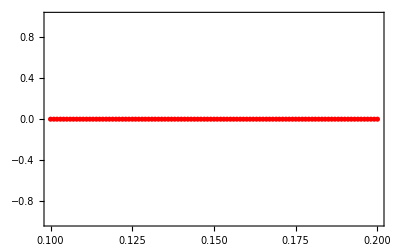

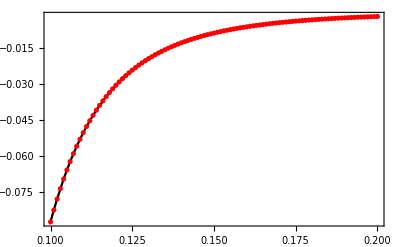

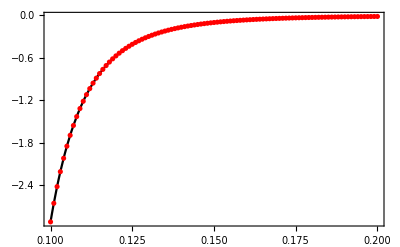

-Graphics-

```mathematica
ClearAll["Global`*"]
wd=SetDirectory@NotebookDirectory[];

(* -139.679800 0.000000 -17.653344 -198.914690 0.000000 *)
(* -0.023101 0.000000 0.015597 0.003139 0.035343 *)

c0data = Import[wd<>"/c0.dat"][[2;;102,{1,3}]];
c1data = Import[wd<>"/c1.dat"][[2;;102,{1,3}]];
c2data = Import[wd<>"/c2.dat"][[2;;102,{1,3}]];
c3data = Import[wd<>"/c3.dat"][[2;;102,{1,3}]];
c4data = Import[wd<>"/c4.dat"][[2;;102,{1,3}]];

Tavg=0.150030572105238;

c0=Interpolation[c0data,Method->"Spline"];
c1=Interpolation[c1data,Method->"Spline"];
c2=Interpolation[c2data,Method->"Spline"];
c3=Interpolation[c3data,Method->"Spline"];
c4=Interpolation[c4data,Method->"Spline"];

c0[Tavg]/Tavg^4
c1[Tavg]/Tavg^3
c2[Tavg]/Tavg^4
c3[Tavg]/Tavg^4
c4[Tavg]/Tavg^5

Show[{{Plot[c0[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[c0data,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[c1[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[c1data,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[c2[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[c2data,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[c3[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[c3data,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[c4[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[c4data,Frame->True,PlotStyle->Red,ImageSize->400]}}]
```

-0.0231009

0.

0.0155966

0.00313919

0.0353432

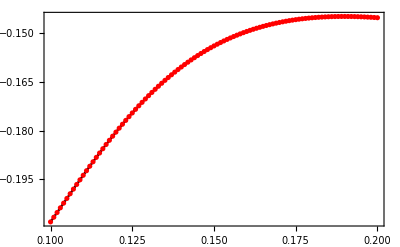

-Graphics-

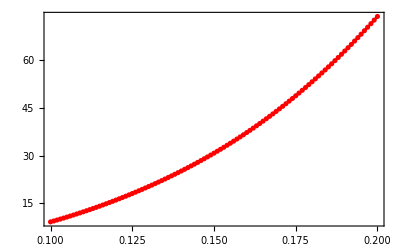

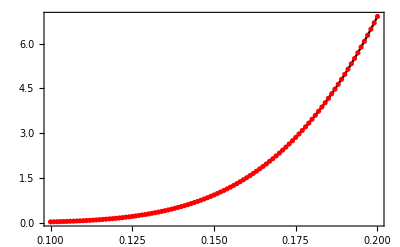

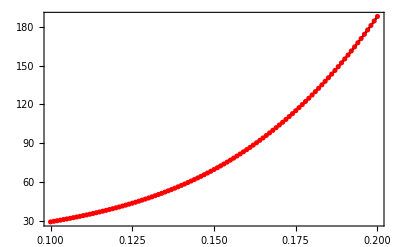

```mathematica
ClearAll["Global`*"]
wd=SetDirectory@NotebookDirectory[];

(* -139.679800 0.000000 -17.653344 -198.914690 0.000000 *)
(* -0.023101 0.000000 0.015597 0.003139 0.035343 *)

Fdata = Import[wd<>"/F.dat"][[2;;102,{1,3}]];
Gdata = Import[wd<>"/G.dat"][[2;;102,{1,3}]];
betabulkdata = Import[wd<>"/betabulk.dat"][[2;;102,{1,3}]];
betaVdata = Import[wd<>"/betaV.dat"][[2;;102,{1,3}]];
betapidata = Import[wd<>"/betapi.dat"][[2;;102,{1,3}]];

Tavg=0.150030572105238;

F=Interpolation[Fdata,Method->"Spline"];
G=Interpolation[Gdata,Method->"Spline"];
betabulk=Interpolation[betabulkdata,Method->"Spline"];
betaV=Interpolation[betaVdata,Method->"Spline"];
betapi=Interpolation[betapidata,Method->"Spline"];

F[Tavg]*Tavg
G[Tavg]
betabulk[Tavg]*Tavg^4
betaV[Tavg]*Tavg^3
betapi[Tavg]*Tavg^4

Show[{{Plot[F[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[Fdata,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[G[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[Gdata,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[betabulk[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[betabulkdata,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[betaV[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[betaVdata,Frame->True,PlotStyle->Red,ImageSize->400]}}]
Show[{{Plot[betapi[T],{T,0.1,0.2},PlotRange->All,Frame->True,PlotStyle->Black,ImageSize->400],ListPlot[betapidata,Frame->True,PlotStyle->Red,ImageSize->400]}}]
```